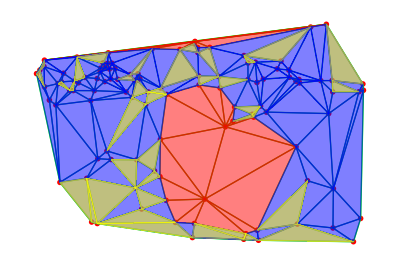

-Graphics-

```mathematica
images={-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-};

imageno=12;
img=images[[imageno]];
(*im=RemoveBackground[img];*)
im=RemoveBackground[img,{Blue,0.40}];
ima=EdgeDetect[im];
cen=ComponentMeasurements[ima,{"Centroid"},#Holes==1&&10<#Area&&#AdjacentBorderCount==0&];

VERHO=ComponentMeasurements[ima,{"ConvexVertices"},#Holes==1&&#Area≥10&&#AdjacentBorderCount==0&];
VerHo=Flatten[VERHO/.Rule-> List,2];
{ranvar,verho}=Partition[VerHo,2,2,1,{}]~Flatten~{2}; 

HighlightImage[ima,Polygon@verho];

b=Flatten[cen/.Rule-> List,2]; 

(*sort out even and odd element, even elements contain coordinate for hole*)
{x,y}=Partition[b,2,2,1,{}]~Flatten~{2}; 
Length[Flatten[y]];
(*y : hole centroid location*)
dm=DelaunayMesh[y];
MeshCellCount[dm,2];

v=MeshPrimitives[dm,0];
t=MeshPrimitives[dm,2];

vedg=Length[Position[Level[t,{2}],#]]&/@Level[v,{2}];
mv=Max[vedg];
mnloc=Flatten[Position[vedg,mv]];
mntri=Flatten[Position[ContainsAny[#,Level[v[[mnloc]],{2}]]&/@Level[t,{2}],True]];

nc=t[[mntri]]; (* nucleus *)
Length[nc] ;
n=Level[v[[mnloc]],{2}] ;(* point in nucleus*)





(*start growing vertex based spoke*)
listalltrian=Flatten[Position[ContainsAny[#,Level[v,{2}]]&/@Level[t,{2}],True]];
listalltrian=Complement[listalltrian,mntri];
nucleuspoints=Complement[Flatten[Level[nc,{2}],1],n];(* nucleuspoints: vertex of the MN region*)
onetime=1;
nspoke=RandomInteger[{0,0},{Length[nucleuspoints],1}];
i=1;
(*growing spoke*)


(*Vertex-Based Spoke*)

While[i<Length[nucleuspoints]+1,

point={nucleuspoints[[i]]};
othernucleuspoint=Complement[nucleuspoints,point];
triofpoint=Flatten[Position[ContainsAny[#,point]&/@Level[t,{2}],True]];
triofothernupoint=Flatten[Position[ContainsAny[#,othernucleuspoint]&/@Level[t,{2}],True]];
list2spokeofpoint=Complement[triofpoint,triofothernupoint];
listalltrian=Complement[listalltrian,list2spokeofpoint];

(*edge based triangle*)
list1edgebasedspoketrian=Complement[triofpoint,list2spokeofpoint,mntri];

continue=True;

If[list2spokeofpoint=={},continue=False,
listnspoke=list2spokeofpoint[[1]];
onepoint=point;
Part[nspoke,i]={listnspoke};
(*nspokestore={listnspoke};*)
listpoint=point];


While[continue,

nextpoint=Level[t[[listnspoke]],{2}];

nextpoint=Complement[nextpoint,onepoint];

nextfirstpoint={nextpoint[[1]]};

listpoint=Union[listpoint,nextfirstpoint];

otherpoint=Complement[nextpoint,nextfirstpoint];
triofnextpoint=Flatten[Position[ContainsAny[#,nextfirstpoint]&/@Level[t,{2}],True]];

triofotherpoint=Flatten[Position[ContainsAny[#,otherpoint]&/@Level[t,{2}],True]];

newspokes=Complement[triofnextpoint,triofotherpoint];
If[newspokes=={},Break[]];
listnspoke=newspokes[[1]];

onepoint=nextfirstpoint;

Part[nspoke,i]=Union[Part[nspoke,i],{listnspoke}];
(*nspokestore=Union[nspokestore,{listnspoke}];*)

If[Length[triofnextpoint]≤6, continue=False,True];
];
If[Part[nspoke,i]=={0},Part[nspoke,i]={},True];
i=i+1;
];


nspokelist=DeleteDuplicates[Flatten[nspoke,2]];


(*EDGE-BASED SPOKE*)
(* Matrix of zeros to store value*)
edgespokelist={0};


(*find all the triangles bordering the nucleus If[newspokes=={},Break[]];*)
For[i=1,i<Length[nc]+1,i++,
tr2=Part[nc,i];
po=Flatten[Position[Level[t,{2}],Level[tr2,{2}]]];
p2=Level[tr2,{2}];
sp1=Complement[p2,n];

l1p=Complement[Flatten[Position[ContainsAll[#,sp1]&/@Level[t,{2}],True]],po];
If[i==1,edgespokelist=l1p,edgespokelist=Join[edgespokelist,l1p]];
choose1point=sp1[[1]];
If[choose1point=={},Break[]];
other2point=Complement[Flatten[Level[t[[l1p]],{2}],1],{choose1point}];
(*construct trinagle contain 2 points and return postion of trinagle*)
nexttripo=Complement[Flatten[Position[ContainsAll[#,other2point]&/@Level[t,{2}],True]],l1p];
cont=True;
edgespokelist=Join[edgespokelist,nexttripo];
thirdpoint=Complement[other2point,sp1];
fourthpoint=Complement[Flatten[Level[t[[nexttripo]],{2}],1],other2point];
next2point=Join[fourthpoint,thirdpoint];
previoustriangle=nexttripo;
e=1;
While[cont,
previoustriangle=Join[previoustriangle,nexttripo];
If[Mod[e,2]==0,onenewpoint=Part[next2point,1],onenewpoint=Part[next2point,2]];
If[onenewpoint=={},cont=False];
e=e+1;
nexttrianglepo=Complement[Flatten[Position[ContainsAll[#,next2point]&/@Level[t,{2}],True]],previoustriangle];
nextother2point=Complement[Flatten[Level[t[[nexttrianglepo]],{2}],1],{onenewpoint}];
new1stpoint=Complement[nextother2point,next2point];
new2ndpoint=Complement[Flatten[Level[t[[nexttrianglepo]],{2}],1],next2point];


next2point=Join[new1stpoint,new2ndpoint];
previoustriangle=Join[previoustriangle,nexttrianglepo];
edgespokelist=Join[edgespokelist,nexttrianglepo];
If[new1stpoint=={} || new2ndpoint=={}  ,cont=False];
]
]

edgespokelistsorted=Complement[edgespokelist,mntri];
nspokelistsorted=Complement[nspokelist,mntri];
(*
  Yellow regions are vertex-based spokes
Blue regions are edge-based spokes 
*)
t1sp=Graphics[{Red,{PointSize[0.01],Point[y]},Green,MeshPrimitives[dm,1],{Opacity[0.5],EdgeForm[{Thick,Red}],FaceForm[Red],nc,EdgeForm[{Thick,Blue}],FaceForm[Blue],t[[edgespokelistsorted]],EdgeForm[{Thick,Yellow}],FaceForm[Yellow],t[[nspokelistsorted]]}}]
Show[img,t1sp, ImageSize->500]
```